Getting the data...

Done.

2. d500k1e005g01a002f1E$200K

μ_η

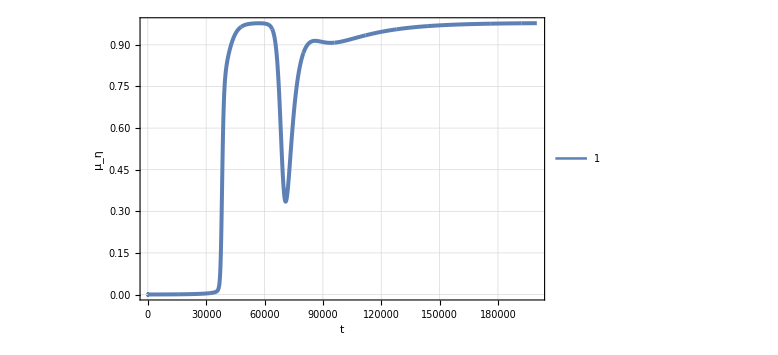

=========================================

3. d500k1e005g01a002i10f1E$200K - error (Chart #5) should look like that.

μ_η

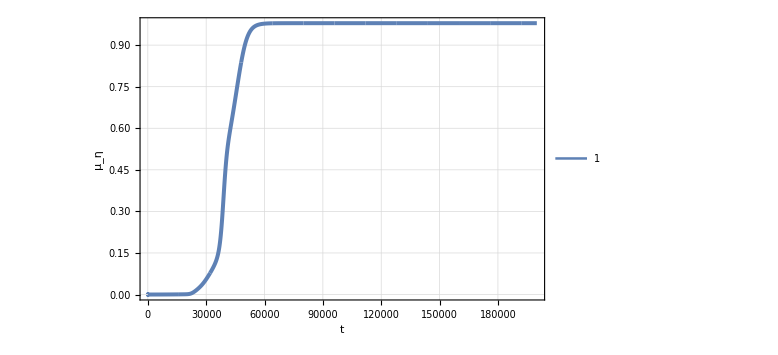

=========================================

4. d500k1e005g01a005f1E$200K

μ_η

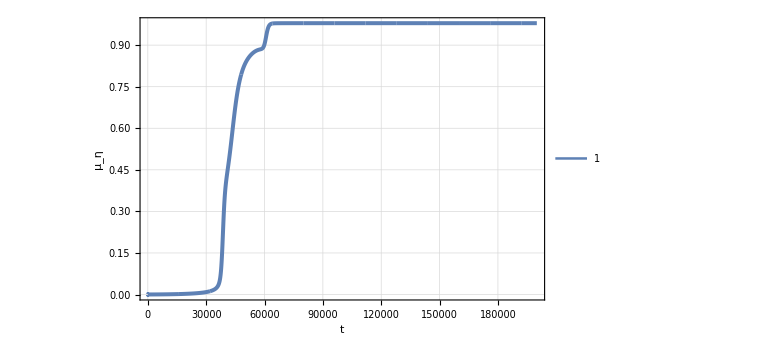

=========================================

6. d500k1e01g01a005f1E$200K - error (Chart #1) should look like that.

μ_η

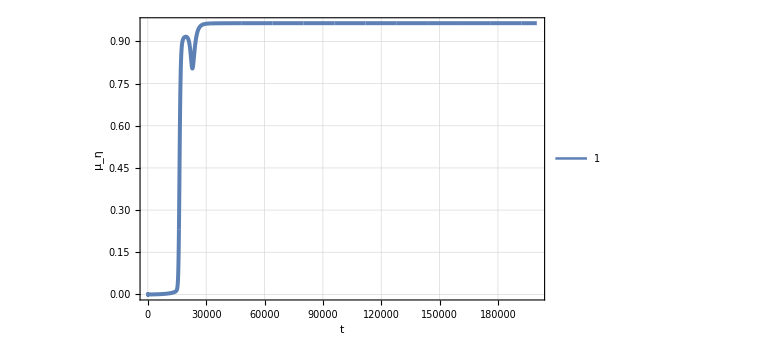

=========================================

=========================================

=========================================

μ_η

-Graphics-

=========================================

σ_η

-Graphics-

=========================================

μ_ζ

-Graphics-

=========================================

σ_ζ

-Graphics-

=========================================

u_total

-Graphics-

=========================================

food

-Graphics-

=========================================

waste

-Graphics-

=========================================

```mathematica
(* Error in: mp_d500k1e01g01a005i10f1T, mp_d500k1e01g01a005i10f1P, mp_d500k1e01g01a005i10f1E *)
(* Based on mp_d500k1e01g01a005 instead of mp_d500k1e01g01a005i10 *)
(* Results in Chart #1 (error) == Chart #6 and in Chart #03 == Chart # 05 (error)  *)

Print["Getting the data..."];
Get["C:\\GitHub\\CoreClm\\Math\\odePackChartSupport.m"];
Get["C:\\GitHub\\FindUniversity\\ClmFsharp\\ISSOL2023\\EeInf\\allData__200K.m"];
Print["Done."];

dataSource = { (* d500k1e01g01a005i10f1E$200K, *) d500k1e005g01a002f1E$200K,d500k1e005g01a002i10f1E$200K,d500k1e005g01a005f1E$200K,(* d500k1e005g01a005i10f1E$200K, *) d500k1e01g01a005f1E$200K };

divisor = 1;

(* { d500k1e01g01a005i10f1E$200K,d500k1e005g01a002f1E$200K,d500k1e005g01a002i10f1E$200K,d500k1e005g01a005f1E$200K,d500k1e005g01a005i10f1E$200K,d500k1e01g01a005f1E$200K} *)

(*
Print["1. ERROR: d500k1e01g01a005i10f1E$200K"];
plotCombinedChart[{d500k1e01g01a005i10f1E$200K},2,Subscript["μ","η"],divisor];
*)

Print["2. d500k1e005g01a002f1E$200K"];
plotCombinedChart[{d500k1e005g01a002f1E$200K},2,Subscript["μ","η"],divisor];

Print["3. d500k1e005g01a002i10f1E$200K - error (Chart #5) should look like that."];
plotCombinedChart[{d500k1e005g01a002i10f1E$200K},2,Subscript["μ","η"],divisor];

Print["4. d500k1e005g01a005f1E$200K"];
plotCombinedChart[{d500k1e005g01a005f1E$200K},2,Subscript["μ","η"],divisor];

(*
Print["5. ERROR: d500k1e005g01a005i10f1E$200K"];
plotCombinedChart[{d500k1e005g01a005i10f1E$200K},2,Subscript["μ","η"],divisor];
*)

Print["6. d500k1e01g01a005f1E$200K - error (Chart #1) should look like that."];
plotCombinedChart[{d500k1e01g01a005f1E$200K},2,Subscript["μ","η"],divisor];

(* ================================================== *)
Print[sep];
Print[sep];

plotCombinedChart[dataSource,2,Subscript["μ","η"],divisor];
plotCombinedChart[dataSource,3,Subscript["σ","η"],divisor];
plotCombinedChart[dataSource,4,Subscript["μ","ζ"],divisor];
plotCombinedChart[dataSource,5,Subscript["σ","ζ"],divisor];
plotCombinedChart[dataSource,7,Subscript["u","total"],divisor];
plotCombinedChart[dataSource,8,"food",divisor];
plotCombinedChart[dataSource,9,"waste",divisor];
```